# 2. Secant Method

```mathematica
secant[f_,a0_,b0_,n_]:= Module[{},p0=N[a0];
p1 = N[b0];
If[f[p0]*f[p1]>0,Print["Secant method cannot be applied"];
Return[]];
Print["________________________________________"];
Print["S.No.", "            ","P0","              ","P1"];
Print["________________________________________"];
i=1;
While[i<=n,p2 = N[p1-((p1-p0)*f[p1]/(f[p1]-f[p0]))];
Print[i, "            ",p0,"              ",p1];
i++;
p0=p1;
p1=p2];
Print["The root of the equation is : ", p2];
Plot[f[x],{x,-3,3},GridLines->Automatic,GridLinesStyle->Directive[Black,Dashed],PlotStyle->{Thickness[0.004],Magenta},PlotLegends->{f[x]},Frame->True]]
```

## Question - 1

________________________________________

S.No.            P0              P1

________________________________________

1            1.              2.

2            2.              1.57143

3            1.57143              1.70541

4            1.70541              1.73514

5            1.73514              1.732

The root of the equation is : 1.73205

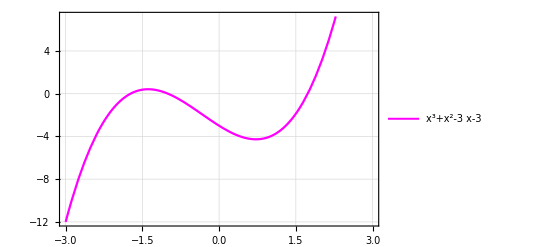

```mathematica
f[x_] := x^3 +x^2-3*x-3
secant[f,1,2,5]
```

## Question-2

________________________________________

S.No.            P0              P1

________________________________________

1            1.              2.

2            2.              1.57143

3            1.57143              1.72857

4            1.72857              1.77564

5            1.77564              1.76759

The root of the equation is : 1.76787

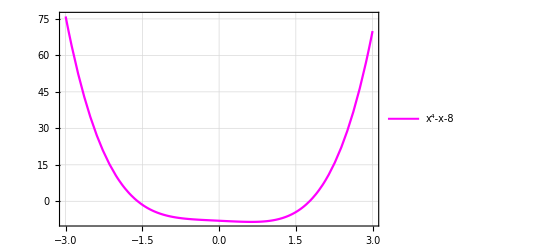

```mathematica
f[x_] := x^4-x-8
secant[f,1,2,5]
```

## Question - 3

4-4 x+x^2

________________________________________

S.No.            P0              P1

________________________________________

1            2.              2.5

2            2.5              2.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

3            2.              2.

4            2.              Indeterminate

5            Indeterminate              Indeterminate

The root of the equation is : Indeterminate

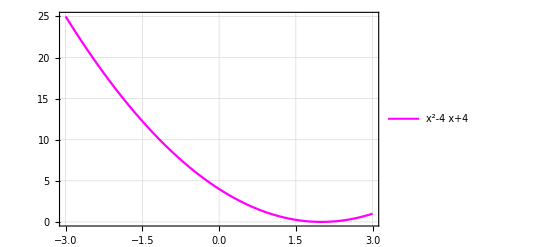

```mathematica
f[x_] = x^2-4x+4
secant[f,2,2.5,5]
```

## Question -4

-8 x-x^2+x^3

________________________________________

S.No.            P0              P1

________________________________________

1            1.              4.

2            4.              2.

3            2.              2.85714

4            2.85714              4.39024

5            4.39024              3.16833

The root of the equation is : 3.29775

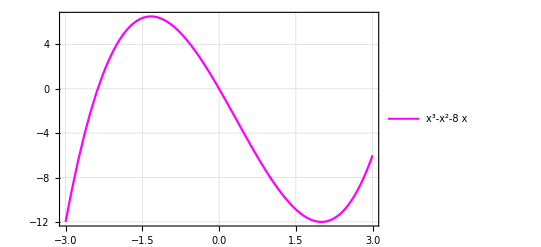

```mathematica
f[x_] = x^3 - x^2-8*x
secant[f,1,4,5]
```